```mathematica
ClearAll["Global`*"];
(*Na bloczku o promieniu R=10 cm i momencie bezwładności
I₀=0,01 kg·m.b2 jest nawinięta nić, na końcu której wisi ciało o masie
m=40 g. Jaką prędkość kątową ω będzie miał bloczek w chwili, gdy
ciało opuści się na odległość h? Sporządzić wykres zależności ω od h
dla h zmieniającego się od 10 cm do 80 cm.*)
```

```mathematica
ΔEp=m ×g×h;
Ek=(m ×v^2)/2;
Ekobr=(Io ×ω^2)/2;
```

```mathematica
v=ω×R;
```

```mathematica
rown1=Solve[ΔEp==Ek+Ekobr,ω]
```

{{ω→-(√2 √g √h √m)/(√(Io+m R^2))},{ω→(√2 √g √h √m)/(√(Io+m R^2))}}

```mathematica
ω=ω/. rown1[[2,1]]
```

(√2 √g √h √m)/(√(Io+m R^2))

```mathematica
R= 0.1; (* m *)
```

```mathematica
Io=0.01; (* kg m^2 *)
```

```mathematica
m= 0.04; (* kg *)
```

```mathematica
g=9.81 ;(* m/s^2 *)
```

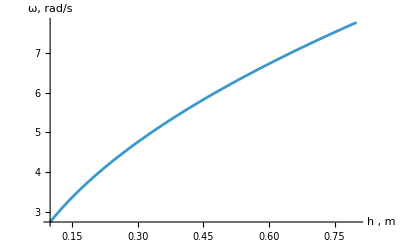

```mathematica
rys2=Plot[ω,{h,0.1,0.8},AxesLabel->{"h , m ","ω, rad/s"}]
```